# Defect Modular Bootstrap

## When the modular matrix has degeneracies modular bootstrap can only do so much to predict the the topological lines of the theory. Here we use a version of Breadth First Search to resolve the ambiguities.

## Modular Bootstrap

We will do this example on the folded Tricritical Ising CFT, but the parameters will be documented so that one can change them.

### Defining Folded Tricritical Ising Modular Data

c =   7/10

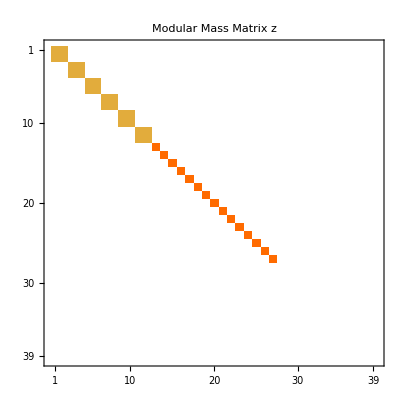

```mathematica
(* Define Tricritical Ising Parameters *)
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(p'-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[p'], Table[{p'/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];
(* Labels of folded Tricritical Ising primaries under the fixed point chiral algebra *)
i=({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);
(* Their Conformal Weights *)
ho[a_]:=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
(* Modular T-Matrix *)
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:= 
(sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+
sv[a[[1]],b[[1]]]sv[a[[2]],b[[1]]]a[[3]]Abs[b[[3]]]-1+
sv[a[[1]],b[[1]]]sv[a[[1]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 
1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+
1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+
1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+
1/8 a[[3]]b[[3]]Total[(sv[a[[1]],#] tv[#]^2 sv[#,b[[1]]])&/@H]Exp[π ⅈ(hv@@(a[[1]]) + hv@@(b[[1]])-cv/12)]Abs[a[[3]]]-2 Abs[b[[3]]]-2;
s=FullSimplify[Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}],ComplexityFunction->LeafCount];
(* Modular Mass Matrix *)
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
MatrixPlot[z,PlotLabel->"Modular Mass Matrix z"]
```

### Obtaining Modular Bootstrap Equations

```mathematica
SolveModularBootstrap[z_,s_]:=Module[
{X,x,nz, st=ConjugateTranspose[s],m,coeff,A, eqn,multipliers,basis},
Needs["math4ti2`"];

(* Get Nonzero positions on the Mass Matrix and replace them with variables *)
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=st. ReplacePart[z,Thread[nz->X]] . s//Flatten;

(* Extract the coefficients for each variable in the S transformed Mass Matrix *)
coeff= CoefficientArrays[m,X][[2]]//Normal//N//Chop;

(* Pick the maximum number of independent equations and invert them *)
A=Chop@Inverse@N@coeff[[Flatten[FirstPosition[#,1]&/@DeleteCases[Chop@RowReduce@N@Transpose@coeff,{0..}]]]];

(* Plug them back in to the S-Transformed Modular Matrix to obtain constraints *)
m=Chop[N[coeff.A]].X;
A=RootApproximant[A];
eqn=DeleteDuplicates@Rationalize@Chop@Expand[#>=0&/@m];

(* Rescale any variables that need it so that the system has integer coefficients *)
multipliers=Min@Cases[eqn,(a_.*#)>=0:>a]^-1&/@X;
eqn=(#[[0]][Subtract@@#//ExpandAll,0])&/@(eqn/. Thread[X->multipliers*X]);

(* Use Z-Solve to find a basis of simple objects *)
basis =math4ti2`zsolve[eqn][[2]];
A. (multipliers*#)&/@basis //FullSimplify
];
families=Sort[SolveModularBootstrap[z,s],#1[[1]] <= #2[[1]]&];
families//Transpose//MatrixForm
noninvertibleFamilies=Select[families,#[[1]]!=1&];
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Resolving Ambiguities

As we can see from the answers above for part of the primaries the action of the defects is ambiguous and we really only know the trace. Yet we have a lot of data, perhaps enough to fully constrain the action on the primaries (up to a basis choice). To do this we will use fusion rules. These are highly constrained also simply by looking at the action in the nondegenerate primaries. Then we will search fusion rules for consistencies using a version of BFS.

### Defect Manipulations

Since we don’t need a really big matrix to store the action of the defects, we will instead opt to store them using a list of 1x1 and 2x2 matrices depending on which are ambiguous or not. So we can define an associative operation for the tensor product!!

```mathematica
(* Define a Defect Fusion Product Operation *)
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=Which[MatrixQ[#[[1]]]&&MatrixQ[#[[2]]],#[[1]].#[[2]], (!MatrixQ[#[[1]]])||(!MatrixQ[#[[2]]]),#[[1]]*#[[2]]]&/@Transpose[{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]

(* A couple of helper functions that can be applied to Lines *)
tr[x_]:=Which[MatrixQ[x],Tr[x],!MatrixQ[x],x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],!MatrixQ[x],1/x];
ShowLine[L_]:=MatrixForm[MatrixForm/@L];

(* This mask tells us if the current primary is degenerate *)
degMask=Thread[families[[1]]!=1];
degPos=Flatten@Position[degMask,True];
nondegPos=Flatten@Position[Not/@degMask,True];
deg[x_]:=degMask[[x]];
degNum=Total@Boole@degMask;
primNum=Total@Boole@degMask;
famNum=Length@families;
familiesNondeg=families[[All,nondegPos]];
```

### Invertible Lines

```mathematica
GetInvertibleLines[]:=Module[
{i={{1,0},{0,1}},
a={{1,0},{0,-1}},
b={{0,1},{1,0}},
c={{0,1},{-1,0}},
L1,Lσ,Lχ},
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,a,a,a,c,c,a,a,c,c,a,c,c,c,c,-a};
{L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗Lχ⊗Lχ,Lχ,Lχ⊗Lχ⊗Lχ}
];

(* Extract the invertible Lines *)
Li=GetInvertibleLines[];

(* Obtain a general Gauge Transformation that preserves the invertible Lines *)
Lp=Array[Which[!deg[#],1,deg[#],{{P[#,1] ,P[#,2] },{P[#,3],P[#,4]}}]&,famNum];
Lp=(Lp //.{ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@Li]==0],Backsubstitution->True]]})[[1]];
Lpp=Lp//Flatten//Variables;
(* Checks if Lp is invertible for a given numerical set of P variables *)
With[{flat=Rationalize@N@Flatten@Cases[Lp,_?MatrixQ]},AA=Outer[D,flat,Lpp];CC=flat/. Thread[Lpp->0]];
LpInvertibleQ[v_]:=AllTrue[Partition[AA.v+CC,4],Det@Partition[#,2]!=0&];

(* These are Queries for if a line is related by conjugation of invertible defects, or by a change of Gauge, or both *)
conjugateOrbit[x_]:=conjugateOrbit[x]=Rationalize@N[#⊗x⊗#]&/@Li;
ConjugateOrbitQ[x_,y_]:=MemberQ[conjugateOrbit[x],Rationalize@N[y]];
leftOrbit[x_]:=leftOrbit[x]=Rationalize@N[#⊗x]&/@Li;
LeftOrbitQ[x_,y_]:=MemberQ[leftOrbit[x],Rationalize@N[y]];
rightOrbit[x_]:=rightOrbit[x]=Rationalize@N[x⊗#]&/@Li;
RightOrbitQ[x_,y_]:=MemberQ[rightOrbit[x],Rationalize@N[y]];
OrbitQ[x_,y_]:=Or[RightOrbitQ[x,y],LeftOrbitQ[x,y],ConjugateOrbitQ[x,y]];
(* Calculates the nullspace of the Jacobian of Lp x - x Lp, and if it is empty then there is no gauge transformation *)
gaugeNullSpace[x_,y_]:=gaugeNullSpace[x,y]=NullSpace@Outer[D,Rationalize@Flatten[N[Lp⊗x-y⊗Lp]],Lpp]; 
GaugeQ[x_,y_]:=AnyTrue[gaugeNullSpace[x,y],Norm[#]>0&&Det[Partition[#,2]]!=0&];
GaugeQ[x_,y_]:=Module[
{ns=gaugeNullSpace[x,y]},
Which[
ns==={},False,
Length@ns ==Length@Lpp,True,
True, LpInvertibleQ[RandomReal[{-1,1},Length[ns]].ns]
]];
(* Combines all queries *)
OrbitGaugeQ[x_,y_]:=OrbitQ[x,y]||GaugeQ[x,y];

(* Returns conditions for line x to be related to line y by a valid gauge transformation *)
FindGaugeRelations[x_,y_]:=Reduce[And@@(Thread[Flatten[N[Lp⊗x - y⊗Lp]]==0]~Join~Thread[Lpp!=0]),Lpp,Complexes,Backsubstitution->True];
```

### Search Fusion Rules

Since we can obtain some partial information for the fusion rules among defects belonging to each family we can extract and list them in the following

```mathematica
(* Takes a matrix M and a vector v and finds all possible nonnegative integer combinations of rows of M that sum to v *)
FindIntegerCombinations[M_,v_]:=Module[
{n=Length[M],m=Length[v],MT=Transpose[N[M]],ubounds,results={}},

(* Use linear programming to estimate the maximum number a row can be added in a solution for v *)
ubounds=Table[Module[{sol},
sol=Quiet[LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]]
,{i,n}];

(* Explore the rest recursively until you hit zero *)
enumerate[rem_,idx_,current_]:=Which[idx>n,If[Chop[N[rem]]==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results
];

(* Store maximum possible fusion pathways between families *)
(*fusionPathways=ParallelArray[FindIntegerCombinations[familiesNondeg//N,familiesNondeg[[#1]]*familiesNondeg[[#2]]//N]&,{famNum, famNum}];*)
```

### Constrain Using Invertible Defect Fusion

Use fusion rules with invertible defects to constrain the possible candidates for lines in a family up to fusion by invertible and gauge transformations

```mathematica
(* Functions to create a defect with free variables and given traces, as well to extract the variables *)
l[traces_,var_]:= Array[Which[!deg[#],traces[[#]],deg[#],{{var[#,1] ,var[#,2] },{var[#,3],traces[[#]]-var[#,1]}}]&,Length@traces];
getVars[x_]:=x//Flatten//Variables;

(* Cleans up some variables *)
CanonicalizeVars[list_]:=Array[i|->Module[{vars},
vars=getVars@list[[i]];
list[[i]]/.MapIndexed[#->#[[0]][i,#2[[1]]]&,vars]],
Length@list];

(* Given a defect with free variables, it outputs a list of the variables that are pure gauge *)
FindGaugeParams[x_]:=Module[
{vars=getVars@x,u},
Pick[vars,GaugeQ[x,x/. #->2]&/@vars]
];

(* Provide candidates for the representation of a defect line up to fusion with invertible lines and gauge transformation *)
ConstrainWithInvertibles[traces_,var_]:=Module[
{ defect=l[traces,var],vars,products,fusions,result},
vars=getVars[defect];
SetAttributes[var,NHoldAll];

(* Calculate the possible fusion channels with the invertible defects *)
products=(#⊗defect)&/@Li;
fusions=MapThread[{N[tr/@#1,30],FindIntegerCombinations[familiesNondeg,Pick[#2,Not/@degMask]]}&,{products,products}]//DeleteDuplicates;
fusions=Transpose[{fusions[[All,1]],N[#.families,30]&/@#}]&/@Tuples[fusions[[All,2]]];
 
(* Convert to equations for their traces, then solve and plug back in *)
fusions=Flatten@#&/@(Thread[#[[1]]==#[[2]]]&/@Transpose[#]&/@#&/@fusions);
result=Flatten[defect//.#&/@DeleteCases[(Quiet@Solve[#,vars])&/@fusions,{}],1];

(*Convert numerical constants back to algebraic form,preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[FullSimplify@result,OrbitGaugeQ]
];
```

### Constrain Using

# OLD STUFF

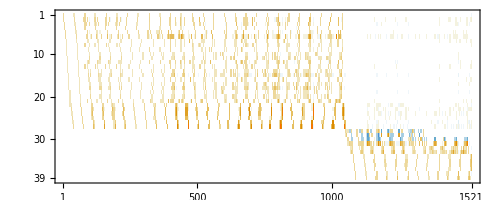

```mathematica
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=ConjugateTranspose[s] . ReplacePart[z,Thread[nz->X]] . s  //Flatten;
A=CoefficientArrays[Thread[m==0],X][[2]]//Simplify//Normal;
a=(A[[#,All]]&/@(Flatten[FirstPosition[#,1]&/@ RowReduce[Transpose[Chop[N[A]]]]]) )//FullSimplify;
Transpose[N[A]]//RowReduce//MatrixPlot
a//MatrixPlot
```

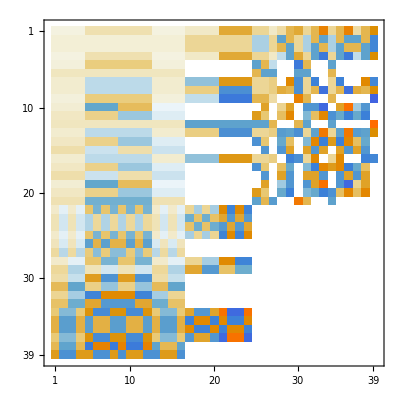

-Graphics-

```mathematica
Organize[e_]:=Module[{l,r},
l=e[[1]];
r=e[[2]];
e[[0]][(l-r)//ExpandAll,0]
];
b=Inverse[N[a]]//Chop;
b=RootApproximant/@b;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.X]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
mx=(Min [Cases[eqn, (a_. * #)>= 0 :>a]])^-1&/@X;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.(mx*X)]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
eqn=Organize/@eqn;
eqn//MatrixForm; 
B=Table[Coefficient[eqn[[i]][[1]],X],{i,Length[eqn]}];
B//MatrixPlot;
```

```mathematica
<<math4ti2`
basis =zsolve[eqn][[2]];
basis//MatrixForm
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
d=b. (mx*#) &/@basis //FullSimplify;
d=Sort[d,#1[[1]] <= #2[[1]]&];
d//Transpose//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) |  | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(2 (5+√5))+ | -√(2 (5+√5))+ | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(2 (5+√5))+ | -√(2 (5+√5))+ | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) |  |  | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(2 (5+√5))+ | -√(2 (5+√5))+ | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) |  |  | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FindRowProducts[M_,N_]:=Module[
{m=Length[M],n=Length[N], results={}},
Do[
With[{product=M[[i]]*N[[j]]//Chop},
If[MemberQ[N,product],
AppendTo[results,{i,j,Position[N,product]//Flatten}]]
],{i,1,m},{j,1,n}];
results
]
FusionCandidates=FindRowProducts[d[[;;5,;;24]],d[[All,;;24]]//N//Chop];
FusionCandidates//Length
FusionCandidates//MatrixForm
```

151

(1 | 1 | {1,2}
1 | 2 | {1,2}
1 | 3 | {3}
1 | 4 | {4}
1 | 5 | {5}
1 | 6 | {6,7}
1 | 7 | {6,7}
1 | 8 | {8}
1 | 9 | {9,12}
1 | 10 | {10,11}
1 | 11 | {10,11}
1 | 12 | {9,12}
1 | 13 | {13}
1 | 14 | {14}
1 | 15 | {15}
1 | 16 | {16,17,18,19}
1 | 17 | {16,17,18,19}
1 | 18 | {16,17,18,19}
1 | 19 | {16,17,18,19}
1 | 20 | {20}
1 | 21 | {21,22}
1 | 22 | {21,22}
1 | 23 | {23}
1 | 24 | {24}
1 | 25 | {25,26}
1 | 26 | {25,26}
1 | 27 | {27}
1 | 28 | {28}
1 | 29 | {29}
1 | 30 | {30}
1 | 31 | {31}
1 | 32 | {32}
1 | 33 | {33}
1 | 34 | {34}
1 | 35 | {35}
1 | 36 | {36}
1 | 37 | {37}
1 | 38 | {38}
1 | 39 | {39}
2 | 1 | {1,2}
2 | 2 | {1,2}
2 | 3 | {3}
2 | 4 | {4}
2 | 5 | {5}
2 | 6 | {6,7}
2 | 7 | {6,7}
2 | 8 | {8}
2 | 9 | {9,12}
2 | 10 | {10,11}
2 | 11 | {10,11}
2 | 12 | {9,12}
2 | 13 | {13}
2 | 14 | {14}
2 | 15 | {15}
2 | 16 | {16,17,18,19}
2 | 17 | {16,17,18,19}
2 | 18 | {16,17,18,19}
2 | 19 | {16,17,18,19}
2 | 20 | {20}
2 | 21 | {21,22}
2 | 22 | {21,22}
2 | 23 | {23}
2 | 24 | {24}
2 | 25 | {25,26}
2 | 26 | {25,26}
2 | 27 | {27}
2 | 28 | {28}
2 | 29 | {29}
2 | 30 | {30}
2 | 31 | {31}
2 | 32 | {32}
2 | 33 | {33}
2 | 34 | {34}
2 | 35 | {35}
2 | 36 | {36}
2 | 37 | {37}
2 | 38 | {38}
2 | 39 | {39}
3 | 1 | {3}
3 | 2 | {3}
3 | 3 | {1,2}
3 | 4 | {5}
3 | 5 | {4}
3 | 6 | {6,7}
3 | 7 | {6,7}
3 | 8 | {8}
3 | 9 | {10,11}
3 | 10 | {9,12}
3 | 11 | {9,12}
3 | 12 | {10,11}
3 | 13 | {14}
3 | 14 | {13}
3 | 15 | {15}
3 | 16 | {16,17,18,19}
3 | 17 | {16,17,18,19}
3 | 18 | {16,17,18,19}
3 | 19 | {16,17,18,19}
3 | 20 | {20}
3 | 21 | {23}
3 | 22 | {23}
3 | 23 | {21,22}
3 | 24 | {24}
3 | 25 | {25,26}
3 | 26 | {25,26}
3 | 27 | {28}
3 | 28 | {27}
3 | 29 | {30}
3 | 30 | {29}
3 | 31 | {31}
3 | 32 | {32}
3 | 33 | {33}
3 | 36 | {37}
3 | 37 | {36}
3 | 38 | {38}
3 | 39 | {39}
4 | 1 | {4}
4 | 2 | {4}
4 | 3 | {5}
4 | 4 | {1,2}
4 | 5 | {3}
4 | 6 | {8}
4 | 7 | {8}
4 | 8 | {6,7}
4 | 9 | {13}
4 | 10 | {14}
4 | 11 | {14}
4 | 12 | {13}
4 | 13 | {9,12}
4 | 14 | {10,11}
4 | 32 | {33}
4 | 33 | {32}
4 | 38 | {39}
4 | 39 | {38}
5 | 1 | {5}
5 | 2 | {5}
5 | 3 | {4}
5 | 4 | {3}
5 | 5 | {1,2}
5 | 6 | {8}
5 | 7 | {8}
5 | 8 | {6,7}
5 | 9 | {14}
5 | 10 | {13}
5 | 11 | {13}
5 | 12 | {14}
5 | 13 | {10,11}
5 | 14 | {9,12}
5 | 32 | {33}
5 | 33 | {32}
5 | 38 | {39}
5 | 39 | {38})

## Describing Invertible Defects

```mathematica
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=Which[MatrixQ[#[[1]]]&&MatrixQ[#[[2]]],#[[1]].#[[2]], (!MatrixQ[#[[1]]])||(!MatrixQ[#[[2]]]),#[[1]]*#[[2]]]&/@Transpose[{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]
tr[x_]:=Which[MatrixQ[x],Tr[x],!MatrixQ[x],x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],!MatrixQ[x],1/x];
threshold=24;
di=Select[d,#[[1]]==1&];
dn=Select[d,#[[1]]!=1&];
Y=Array[y,{Length[d]-threshold,3}];
YY=Y//Flatten;
Z=Array[yz,{Length[d]-threshold,3}];
ZZ=Z//Flatten;
P=Array[pp,{Length[d]-threshold,4}];
PP=P//Flatten;
LP=Array[Which[#<=threshold,1,#>threshold,
{{P[[#-threshold,1]] ,P[[#-threshold,2]] },{P[[#-threshold,3]],P[[#-threshold,4]]}}]&,Length[d]];
l[i_,v_:Y]:=Array[Which[#<=threshold,d[[i,#]],#>threshold,
{{v[[#-threshold,1]] ,v[[#-threshold,2]] },{v[[#-threshold,3]],d[[i,#]]-v[[#-threshold,1]]}}]&,Length[d]];
```

```mathematica
FindIntegerCombinations[M_,v_]:=Module[{n=Length[M],m=Length[v],MT,ubounds,results={}},
MT=Transpose[N[M]];
ubounds=Table[Module[{sol},
sol=LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]],{i,n}];
enumerate[rem_,idx_,current_]:=Which[idx>n,If[rem==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results]
```

```mathematica
ii={{1,0},{0,1}};
aa={{1,0},{0,-1}};
bb={{0,1},{1,0}};
cc={{0,1},{-1,0}};
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,aa,aa,aa,cc,cc,aa,aa,cc,cc,aa,cc,cc,cc,cc,-aa};
Di={L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗(Lχ⊗Lχ),Lχ,Lχ⊗(Lχ⊗Lχ)};
LP //.{ToRules[Reduce[And@@Thread[Flatten[(LP⊗# -#⊗LP)&/@Di]==0],PP,Complexes,Backsubstitution->True]]}
fam[x_]:=Which[MemberQ[{3,4},x],3,MemberQ[{5,6},x],4,MemberQ[{7,8},x],5,True,x];
MatrixForm[MatrixForm/@#]&/@Di
ConjugateQ[x_,y_]:=MemberQ[N[(#⊗x)⊗#]&/@Di,y];
GaugeQ[x_,y_]:=!(Solve[And@@(Thread[Flatten[LP⊗x - y⊗LP]==0]~Join~Thread[PP!=0]),PP]==={});
ConjugateGaugeQ[x_,y_]:=Or@@(GaugeQ[#,y]&/@(N[(#⊗x)⊗#]&/@Di));
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,{{pp[1,1],0},{0,pp[1,4]}},{{pp[2,1],0},{0,pp[2,4]}},{{pp[3,1],0},{0,pp[3,4]}},{{pp[4,1],0},{0,pp[4,1]}},{{pp[5,1],0},{0,pp[5,1]}},{{pp[6,1],0},{0,pp[6,4]}},{{pp[7,1],0},{0,pp[7,4]}},{{pp[8,1],0},{0,pp[8,1]}},{{pp[9,1],0},{0,pp[9,1]}},{{pp[10,1],0},{0,pp[10,4]}},{{pp[11,1],0},{0,pp[11,1]}},{{pp[12,1],0},{0,pp[12,1]}},{{pp[13,1],0},{0,pp[13,1]}},{{pp[14,1],0},{0,pp[14,1]}},{{pp[15,1],0},{0,pp[15,4]}}}}

{(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)),(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(1 | 0
0 | 1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(1 | 0
0 | 1)),(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
-1
-1
-1
-1
-1
-1
-1
-1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(1 | 0
0 | 1)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(-1 | 0
0 | -1)),(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
-1
-1
-1
-1
-1
-1
-1
-1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(1 | 0
0 | 1)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(-1 | 0
0 | -1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(1 | 0
0 | -1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(1 | 0
0 | -1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
-1
1
1
-1
-1
1
1
-1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(1 | 0
0 | -1)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(-1 | 0
0 | 1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
-1
1
1
-1
-1
1
1
-1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(1 | 0
0 | -1)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(-1 | 0
0 | 1))}

```mathematica
Family=10;
FusionCandidates={tr/@(Di[[#[[1]]]]⊗l[#[[2]]]⊗Di[[#[[3]]]])//Simplify,FindIntegerCombinations[d[[All,;;threshold]],d[[fam[#[[1]]],;;threshold]]d[[#[[2]],;;threshold]]d[[fam[#[[3]]],;;threshold]]]}&/@Tuples[{Range@Length@Di,{Family},{1}}];
FusionCandidates=FusionCandidates~Join~({tr/@(l[#[[1]]]⊗l[#[[2]]])//Simplify,FindIntegerCombinations[d[[All,;;threshold]],d[[#[[1]],;;threshold]]d[[#[[2]],;;threshold]]]}&/@Tuples[{{Family},{Family}}]);
FusionCandidates=DeleteDuplicates[FusionCandidates];
fusions=Transpose[{FusionCandidates[[All,1]], #.d&/@#}]&/@Tuples[FusionCandidates[[All,2]]];
fusions=Thread[#[[1]]==#[[2]]]&/@Transpose[#]&/@#&/@fusions;
(*fusions=DeleteDuplicates[fusions];*)
```

```mathematica
solns=Solve[And @@(Flatten[#]),YY ]&/@fusions//Simplify;
mask =(#!={})&/@solns;
defects=((Simplify[l[Family]//.#])&/@Pick[solns,mask]);
defects=DeleteDuplicates[Flatten[defects,1],ConjugateGaugeQ];
W=Array[y,{Length@defects,Length@d-threshold,3}];
WW=Flatten/@W;
defects=Array[(defects[[#]]/.Thread[YY->WW[[#]]])&,Length@defects];
rules=Pick[Tuples[FusionCandidates[[All,2]]],mask];
MatrixForm[MatrixForm/@#]&/@defects
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[1,1,2]
5/(4 y[1,1,2]) | 1/2)
(1/2 | y[1,2,2]
5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | 0
y[1,3,3] | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
y[1,6,3] | 1/2 (1-√5))
(1/2 | y[1,7,2]
5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[1,10,2]
5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[1,15,2]
5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[2,1,2]
5/(4 y[2,1,2]) | 1/2)
(1/2 | y[2,2,2]
5/(4 y[2,2,2]) | 1/2)
(1/2 (1+√5) | y[2,3,2]
0 | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
y[2,6,3] | 1/2 (1-√5))
(1/2 | y[2,7,2]
5/(4 y[2,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[2,10,2]
5/(4 y[2,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[2,15,2]
5/(4 y[2,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[3,1,2]
5/(4 y[3,1,2]) | 1/2)
(1/2 | y[3,2,2]
5/(4 y[3,2,2]) | 1/2)
(1/2 (1+√5) | 0
y[3,3,3] | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[3,6,2]
0 | 1/2 (1-√5))
(1/2 | y[3,7,2]
5/(4 y[3,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[3,10,2]
5/(4 y[3,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[3,15,2]
5/(4 y[3,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[4,1,2]
5/(4 y[4,1,2]) | 1/2)
(1/2 | y[4,2,2]
5/(4 y[4,2,2]) | 1/2)
(1/2 (1+√5) | y[4,3,2]
0 | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[4,6,2]
0 | 1/2 (1-√5))
(1/2 | y[4,7,2]
5/(4 y[4,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[4,10,2]
5/(4 y[4,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[4,15,2]
5/(4 y[4,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[5,1,2]
5/(4 y[5,1,2]) | 1/2)
(1/2 | y[5,2,2]
5/(4 y[5,2,2]) | 1/2)
(1/2 (1+√5) | 0
y[5,3,3] | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
y[5,6,3] | 1/2 (1-√5))
(1/2 | y[5,7,2]
5/(4 y[5,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | y[5,10,2]
5/(4 y[5,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[5,15,2]
5/(4 y[5,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[6,1,2]
5/(4 y[6,1,2]) | 1/2)
(1/2 | y[6,2,2]
5/(4 y[6,2,2]) | 1/2)
(1/2 (1+√5) | y[6,3,2]
0 | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
y[6,6,3] | 1/2 (1-√5))
(1/2 | y[6,7,2]
5/(4 y[6,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | y[6,10,2]
5/(4 y[6,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[6,15,2]
5/(4 y[6,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[7,1,2]
5/(4 y[7,1,2]) | 1/2)
(1/2 | y[7,2,2]
5/(4 y[7,2,2]) | 1/2)
(1/2 (1+√5) | 0
y[7,3,3] | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[7,6,2]
0 | 1/2 (1-√5))
(1/2 | y[7,7,2]
5/(4 y[7,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | y[7,10,2]
5/(4 y[7,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[7,15,2]
5/(4 y[7,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[8,1,2]
5/(4 y[8,1,2]) | 1/2)
(1/2 | y[8,2,2]
5/(4 y[8,2,2]) | 1/2)
(1/2 (1+√5) | y[8,3,2]
0 | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[8,6,2]
0 | 1/2 (1-√5))
(1/2 | y[8,7,2]
5/(4 y[8,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | y[8,10,2]
5/(4 y[8,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[8,15,2]
5/(4 y[8,15,2]) | 1/2))}

```mathematica
prods=(tr/@(#[[1]]⊗#[[2]]⊗#[[3]]))&/@Tuples[{defects,defects,Di}]//Simplify//DeleteDuplicates;
combos=#.d&/@#&/@(FindIntegerCombinations[Transpose@Pick[Transpose[d],FreeQ[#//N,_Symbol]&/@#],Pick[#,FreeQ[#//N,_Symbol]&/@#]]&/@prods);
eqns=Or@@#&/@Array[(And@@#&/@(MapThread[Equal, #]&/@Tuples[{{prods[[#]]},combos[[#]]}]))&,Length@prods]//Simplify;
```

```mathematica
simplified=DeleteDuplicates[(defects/.Solve[And@@eqns//Simplify,WW//Flatten,Complexes][[1]]),ConjugateGaugeQ];
MatrixForm[MatrixForm/@#]&/@simplified
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[1,1,2]
5/(4 y[1,1,2]) | 1/2)
(1/2 | y[1,2,2]
5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | y[1,7,2]
5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[1,10,2]
5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[1,15,2]
5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[1,1,2]
5/(4 y[1,1,2]) | 1/2)
(1/2 | y[1,2,2]
5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | y[2,3,2]
0 | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | y[1,7,2]
5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[1,10,2]
5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[1,15,2]
5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[1,1,2]
5/(4 y[1,1,2]) | 1/2)
(1/2 | y[1,2,2]
5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[3,6,2]
0 | 1/2 (1-√5))
(1/2 | y[1,7,2]
5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[1,10,2]
5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[1,15,2]
5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | y[1,1,2]
5/(4 y[1,1,2]) | 1/2)
(1/2 | y[1,2,2]
5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | y[4,3,2]
0 | 1/2 (1+√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[4,6,2]
0 | 1/2 (1-√5))
(1/2 | y[1,7,2]
5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | y[1,10,2]
5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | y[1,15,2]
5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | -y[1,1,2]
-5/(4 y[1,1,2]) | 1/2)
(1/2 | -y[1,2,2]
-5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | y[6,3,2]
0 | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | -y[1,7,2]
-5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -y[1,10,2]
-5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | -y[1,15,2]
-5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | -y[1,1,2]
-5/(4 y[1,1,2]) | 1/2)
(1/2 | -y[1,2,2]
-5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[7,6,2]
0 | 1/2 (1-√5))
(1/2 | -y[1,7,2]
-5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -y[1,10,2]
-5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | -y[1,15,2]
-5/(4 y[1,15,2]) | 1/2)),(1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1-√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
1/2 (1+√5)
(1/2 | -y[1,1,2]
-5/(4 y[1,1,2]) | 1/2)
(1/2 | -y[1,2,2]
-5/(4 y[1,2,2]) | 1/2)
(1/2 (1+√5) | y[8,3,2]
0 | 1/2 (1+√5))
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 (1-√5) | y[8,6,2]
0 | 1/2 (1-√5))
(1/2 | -y[1,7,2]
-5/(4 y[1,7,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -y[1,10,2]
-5/(4 y[1,10,2]) | 1/2)
(1/2 (1-√5) | 0
0 | 1/2 (1-√5))
(1/2 | (√5)/2
(√5)/2 | 1/2)
(1/2 | -(√5)/2
-(√5)/2 | 1/2)
(1/2 (1+√5) | 0
0 | 1/2 (1+√5))
(1/2 | -y[1,15,2]
-5/(4 y[1,15,2]) | 1/2))}

```mathematica
Variables@Flatten@simplified
```

{y[1,1,2],y[1,2,2],y[1,7,2],y[1,10,2],y[1,15,2],y[2,3,2],y[3,6,2],y[4,3,2],y[4,6,2],y[6,3,2],y[7,6,2],y[8,3,2],y[8,6,2]}